# Characters in Jane Austin’s Pride and Prejudice

### Retrieve the book from ExampleData

```mathematica
prideText=ExampleData[{"Text","PrideAndPrejudice"}];
```

```mathematica
Short[prideText]
```

Chapter 1 It is a truth universally ackn…ire, had been the means of uniting them.

### Using TextContents

First 8000 characters of the book

```mathematica
TextContents[StringTake[prideText,8000],"FictionalCharacter"]
```

### Using Wolfram Knowledgebase

#### Book

WolframAlphaQueryParseResults

Pride and Prejudice

```mathematica
Entity["Book","PrideAndPrejudice"]["Dataset"]
```

#### Fictional Character

WolframAlphaQueryParseResults

Mr. Darcy

```mathematica
Entity["FictionalCharacter","FitzwilliamDarcy"]["Dataset"]
```

### Using Wikidata

Here is the Wikidata entity for Pride and Prejudice

```mathematica
ExternalIdentifier["WikidataID","Q170583",<|"Label"->"Pride and Prejudice"|>]
```

ExternalIdentifier[WikidataID,Q170583,<|Label→Pride and Prejudice|>]WikidataPride and Prejudicehttp://www.wikidata.org/entity/Q170583

Here is a dataset of all of the properties for the Wikidata entity for Pride and Prejudice

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q170583",<|"Label"->"Pride and Prejudice","Description"->"novel by Jane Austen"|>]"Wikidata""Pride and Prejudice"http://www.wikidata.org/entity/Q170583,"Dataset"]
```

Here is the Wikidata property for fictional characters

```mathematica
ExternalIdentifier["WikidataID","P674"]
```

ExternalIdentifier[WikidataID,P674]WikidataP674http://www.wikidata.org/entity/P674

Now we have enough information to retrieve Wikidata entities for each character

```mathematica
ppCharacterWikiIDs=WikidataData[ExternalIdentifier["WikidataID","Q170583",<|"Label"->"Pride and Prejudice","Description"->"novel by Jane Austen"|>]"Wikidata""Pride and Prejudice"http://www.wikidata.org/entity/Q170583,ExternalIdentifier["WikidataID","P674"]"Wikidata""P674"http://www.wikidata.org/entity/P674]
```

{ExternalIdentifier[WikidataID,Q2198673,<|Label→Jane Bennet,Description→Pride and Prejudice Character|>]WikidataJane Bennethttp://www.wikidata.org/entity/Q2198673,ExternalIdentifier[WikidataID,Q2207092,<|Label→Mr. Darcy,Description→fictional character from Pride and Prejudice|>]WikidataMr. Darcyhttp://www.wikidata.org/entity/Q2207092,ExternalIdentifier[WikidataID,Q2223341,<|Label→Elizabeth Bennet,Description→fictional character from Pride and Prejudice|>]WikidataElizabeth Bennethttp://www.wikidata.org/entity/Q2223341,ExternalIdentifier[WikidataID,Q2250982,<|Label→George Wickham,Description→fictional character from Pride and Prejudice|>]WikidataGeorge Wickhamhttp://www.wikidata.org/entity/Q2250982,ExternalIdentifier[WikidataID,Q2289525,<|Label→Mr William Collins,Description→fictional character from Pride and Prejudice by Jane Austen|>]WikidataMr William Collinshttp://www.wikidata.org/entity/Q2289525,ExternalIdentifier[WikidataID,Q2337271,<|Label→Lydia Bennet,Description→Pride and Prejudice character|>]WikidataLydia Bennethttp://www.wikidata.org/entity/Q2337271,ExternalIdentifier[WikidataID,Q4390263,<|Label→Charles Bingley,Description→Pride and Prejudice character|>]WikidataCharles Bingleyhttp://www.wikidata.org/entity/Q4390263,ExternalIdentifier[WikidataID,Q6470022,<|Label→Lady Catherine de Bourgh,Description→character from Pride and Prejudice by Jane Austen|>]WikidataLady Catherine de Bourghhttp://www.wikidata.org/entity/Q6470022,ExternalIdentifier[WikidataID,Q6929362,<|Label→Mr Bennet,Description→Pride and Prejudice character|>]WikidataMr Bennethttp://www.wikidata.org/entity/Q6929362,ExternalIdentifier[WikidataID,Q19816980,<|Label→Mary Bennet,Description→Pride and Prejudice character|>]WikidataMary Bennethttp://www.wikidata.org/entity/Q19816980,ExternalIdentifier[WikidataID,Q19816987,<|Label→Catherine Bennet,Description→Pride and Prejudice character|>]WikidataCatherine Bennethttp://www.wikidata.org/entity/Q19816987,ExternalIdentifier[WikidataID,Q19817013,<|Label→Mrs Bennet,Description→Pride and Prejudice character|>]WikidataMrs Bennethttp://www.wikidata.org/entity/Q19817013,ExternalIdentifier[WikidataID,Q64019262,<|Label→Mr. Jones,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMr. Joneshttp://www.wikidata.org/entity/Q64019262,ExternalIdentifier[WikidataID,Q64019263,<|Label→Mrs. Younge,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs. Youngehttp://www.wikidata.org/entity/Q64019263,ExternalIdentifier[WikidataID,Q64019261,<|Label→Mr Philips,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMr Philipshttp://www.wikidata.org/entity/Q64019261,ExternalIdentifier[WikidataID,Q64019264,<|Label→Haggerston,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataHaggerstonhttp://www.wikidata.org/entity/Q64019264,ExternalIdentifier[WikidataID,Q64027362,<|Label→Mr. Dawson,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMr. Dawsonhttp://www.wikidata.org/entity/Q64027362,ExternalIdentifier[WikidataID,Q21775022,<|Label→Caroline Bingley,Description→Pride and Prejudice character|>]WikidataCaroline Bingleyhttp://www.wikidata.org/entity/Q21775022,ExternalIdentifier[WikidataID,Q21775023,<|Label→Georgiana Darcy,Description→Pride and Prejudice character|>]WikidataGeorgiana Darcyhttp://www.wikidata.org/entity/Q21775023,ExternalIdentifier[WikidataID,Q22924649,<|Label→Mr Gardiner,Description→character from Pride and Prejudice by Jane Austen|>]WikidataMr Gardinerhttp://www.wikidata.org/entity/Q22924649,ExternalIdentifier[WikidataID,Q64019239,<|Label→Charlotte Lucas,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataCharlotte Lucashttp://www.wikidata.org/entity/Q64019239,ExternalIdentifier[WikidataID,Q64019242,<|Label→Miss de Bourgh,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMiss de Bourghhttp://www.wikidata.org/entity/Q64019242,ExternalIdentifier[WikidataID,Q64019240,<|Label→Sir William Lucas,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataSir William Lucashttp://www.wikidata.org/entity/Q64019240,ExternalIdentifier[WikidataID,Q64019241,<|Label→Mrs. Hill,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs. Hillhttp://www.wikidata.org/entity/Q64019241,ExternalIdentifier[WikidataID,Q64019246,<|Label→Mr. Denny,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMr. Dennyhttp://www.wikidata.org/entity/Q64019246,ExternalIdentifier[WikidataID,Q64019247,<|Label→Mrs. Hurst,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs. Hursthttp://www.wikidata.org/entity/Q64019247,ExternalIdentifier[WikidataID,Q64019244,<|Label→Colonel Fitzwilliam,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataColonel Fitzwilliamhttp://www.wikidata.org/entity/Q64019244,ExternalIdentifier[WikidataID,Q64019245,<|Label→Mrs Gardiner,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs Gardinerhttp://www.wikidata.org/entity/Q64019245,ExternalIdentifier[WikidataID,Q64019250,<|Label→Mrs Philips,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs Philipshttp://www.wikidata.org/entity/Q64019250,ExternalIdentifier[WikidataID,Q64019248,<|Label→Maria Lucas,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMaria Lucashttp://www.wikidata.org/entity/Q64019248,ExternalIdentifier[WikidataID,Q64019249,<|Label→Mr. Hurst,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMr. Hursthttp://www.wikidata.org/entity/Q64019249,ExternalIdentifier[WikidataID,Q64019255,<|Label→Colonel Forster,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataColonel Forsterhttp://www.wikidata.org/entity/Q64019255,ExternalIdentifier[WikidataID,Q64019252,<|Label→Captain Carter,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataCaptain Carterhttp://www.wikidata.org/entity/Q64019252,ExternalIdentifier[WikidataID,Q64019253,<|Label→Lady Lucas,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataLady Lucashttp://www.wikidata.org/entity/Q64019253,ExternalIdentifier[WikidataID,Q64019258,<|Label→Mary King,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMary Kinghttp://www.wikidata.org/entity/Q64019258,ExternalIdentifier[WikidataID,Q64019259,<|Label→Mrs. Reynolds,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs. Reynoldshttp://www.wikidata.org/entity/Q64019259,ExternalIdentifier[WikidataID,Q64019256,<|Label→Mrs. Forster,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs. Forsterhttp://www.wikidata.org/entity/Q64019256,ExternalIdentifier[WikidataID,Q64019257,<|Label→Mrs. Jenkinson,Description→fictional character from Jane Austen's Pride and Prejudice|>]WikidataMrs. Jenkinsonhttp://www.wikidata.org/entity/Q64019257}

```mathematica
First[ppCharacterWikiIDs]["Label"]
```

Jane Bennet

Get a list of character names

```mathematica
ppCharacterNames=Table[p["Label"],{p,ppCharacterWikiIDs}]
```

{Jane Bennet,Mr. Darcy,Elizabeth Bennet,George Wickham,Mr William Collins,Lydia Bennet,Charles Bingley,Lady Catherine de Bourgh,Mr Bennet,Mary Bennet,Catherine Bennet,Mrs Bennet,Mr. Jones,Mrs. Younge,Mr Philips,Haggerston,Mr. Dawson,Caroline Bingley,Georgiana Darcy,Mr Gardiner,Charlotte Lucas,Miss de Bourgh,Sir William Lucas,Mrs. Hill,Mr. Denny,Mrs. Hurst,Colonel Fitzwilliam,Mrs Gardiner,Mrs Philips,Maria Lucas,Mr. Hurst,Colonel Forster,Captain Carter,Lady Lucas,Mary King,Mrs. Reynolds,Mrs. Forster,Mrs. Jenkinson}

### Break text into 250 word blocks

Use the Partition command to break text into non-overlapping, 250-word blocks

```mathematica
pp250WordBlocks=Partition[TextWords[prideText],250,250,1,{}];
```

```mathematica
Length[pp250WordBlocks]
```

488

```mathematica
First@pp250WordBlocks
```

{Chapter,1,It,is,a,truth,universally,acknowledged,that,a,single,man,in,possession,of,a,good,fortune,must,be,in,want,of,a,wife,However,little,known,the,feelings,or,views,of,such,a,man,may,be,on,his,first,entering,a,neighbourhood,this,truth,is,so,well,fixed,in,the,minds,of,the,surrounding,families,that,he,is,considered,the,rightful,property,of,some,one,or,other,of,their,daughters,My,dear,Mr.,Bennet,said,his,lady,to,him,one,day,have,you,heard,that,Netherfield,Park,is,let,at,last,Mr.,Bennet,replied,that,he,had,not,But,it,is,returned,she,for,Mrs.,Long,has,just,been,here,and,she,told,me,all,about,it,Mr.,Bennet,made,no,answer,Do,you,not,want,to,know,who,has,taken,it,cried,his,wife,impatiently,You,want,to,tell,me,and,I,have,no,objection,to,hearing,it,This,was,invitation,enough,Why,my,dear,you,must,know,Mrs.,Long,says,that,Netherfield,is,taken,by,a,young,man,of,large,fortune,from,the,north,of,England,that,he,came,down,on,Monday,in,a,chaise,and,four,to,see,the,place,and,was,so,much,delighted,with,it,that,he,agreed,with,Mr.,Morris,immediately,that,he,is,to,take,possession,before,Michaelmas,and,some,of,his,servants,are,to,be,in,the,house,by,the,end,of,next,week,What,is,his,name,Bingley,Is,he,married,or,single,Oh,Single,my,dear,to,be}

Look for 2 word sequence. Three occurrences of “Mr. Bennet” in first 250 word block

```mathematica
SequenceCases[pp250WordBlocks⟦1⟧,{"Mr.","Bennet"}]
```

{{Mr.,Bennet},{Mr.,Bennet},{Mr.,Bennet}}

### Count occurrences in each 250 word block

```mathematica
getOccurrences[txtblks_,ngram_]:=
Map[Length[SequenceCases[#,ngram]]&,txtblks]
```

```mathematica
getOccurrences[pp250WordBlocks,{"Mr.","Bennet"}]
```

{3,1,1,2,2,1,1,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,2,0,1,1,3,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,2,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,2,1,2,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,2,1,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0}

### Plot one character

```mathematica
ArrayPlot[{getOccurrences[pp250WordBlocks,{"Mr.","Bennet"}]},ImageSize->Full]
```

-Graphics-

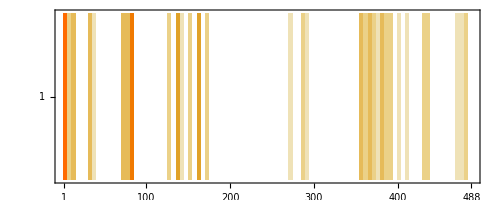

```mathematica
MatrixPlot[{getOccurrences[pp250WordBlocks,{"Mr.","Bennet"}]},ImageSize->Full]
```

### Plot character cooccurrence

This function lets us compare distributions of n-grams and visualize their cooccurrence (or lack thereof)

```mathematica
plotCooccurrences[txtblks_,ngramlist_]:=
MatrixPlot[Map[getOccurrences[txtblks,#]&,ngramlist],ImageSize->Full,AspectRatio->1/8,FrameTicks->{Map[{#,StringRiffle@ngramlist⟦#⟧}&,Range[Length[ngramlist]]],Automatic},ImagePadding->{{110,10},{20,5}}]
```

The Column command lets us combine a number of plots into one figure

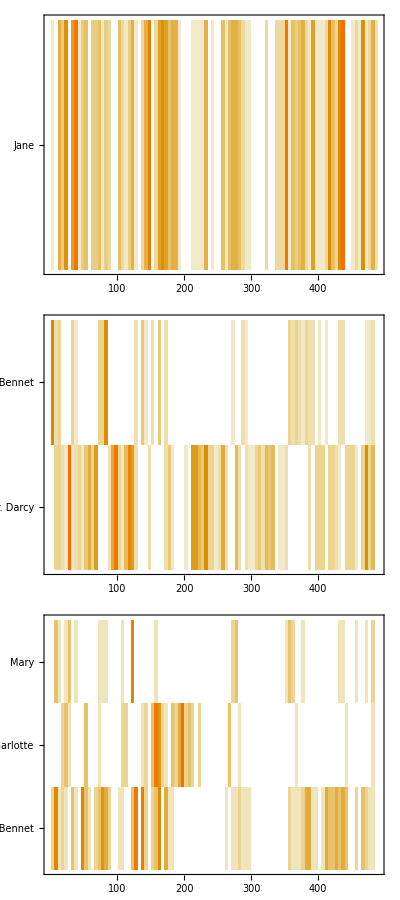

```mathematica
Column[{plotCooccurrences[pp250WordBlocks,{{"Jane"}}],
plotCooccurrences[pp250WordBlocks,{{"Mr.","Bennet"},{"Mr.","Darcy"}}],
plotCooccurrences[pp250WordBlocks,{{"Mary"},{"Charlotte"},{"Mrs.","Bennet"}}]}]
```